## Modèle TBR

### Paramètres connues du système

```mathematica
L=1 (*m*); (*hauteur du réacteur*)
d=0.18 (*m*);(*diamètre de la colonne*)
Ω= Pi (d/2)^2(*m.b2*); (*surface de la colonne*)
dp=2.5 10^-2(*m*); (*diamètre éléments de garnissage*)
Ap=312 (*m.b2int.G-L/m.b3column*);
Debit=50. 10^-6 (*m^3/min*);(*débit de gaz entrant variant de 25 à 100ml/min*)
Qgin=16 Debit/60 (*m.b3/s*); (*débit de gaz entrant dans le réacteur*)
Qlin=(4.5 10^-3)/60(*m.b3/s*); (*débit de liquide entrant dans le réacteur*)

Rg=8.314(*kg m.b2 s-2 K−1 mol−1*); (*constante gaz parfait*)
Tin=25+273.15 (*K*); (*température de travail*)
Pin=101325(*Pa*); (*pression de travail*)
Patm=1(*atm*);
gz=9.81 (*m/s.b2*); (*acc gravité*)

Dco2l=3 10^-5 Exp[-3096/Tin] (*m^2/s*); (*coef diffusion CO2 dans l'eau*)
(*Source : Book,CHEMICAL REACTORS From Design to Operation*)

Dh2l=5.13 10^-9(*m.b2/s*); (*coef diffusion H2 dans l'eau*)
(*Source: https://www.engineeringtoolbox.com/air-diffusion-coefficient-gas-mixture-temperature-d_2010.html*)

ρw=997.13(*kg/m.b3*); (*densité de l'eau à 20°C*)
(*Source: https://www.thermexcel.com/french/tables/eau_atm.htm*)

μw=0.891 10^-3 (*Pa.s*); (*visco de l'eau à 25°C *)(*Source: https://www.thermexcel.com/french/tables/eau_atm.htm*)


Hco2=3.4 10^1 (*mol/m.b3/atm*); (*constante de Henry du CO2 dans l'eau à 25°C*)
Hh2=7.8 10^-1(*mol/m.b3/atm*); (*Constante de Henry de l'H2 dans l'eau à 25°C*)
(*Source: https://www.ready.noaa.gov/documents/TutorialX/files/Chem_henry.pdf*)
```

### Paramètres expérimentaux du système

```mathematica
ϵl=0.015;(*liquid phase*);
ϵg=0.9;(*gas proportion*);
(*klco2 ? pas encore obtenu*)
```

### Initial conditions

```mathematica
yco20=0.2;(*fraction molaire de CO2 à la base de la colonne*)
yh20=0.8;(*fraction molaire d'H2 à la base de la colonne*)
Cco2i=0(*mol/m.b3*); (*Concentration initiale de CO2 dans le liquide*) 
Ch2i=0 (*mol/m.b3*);(*Concentration initiale d'H2 dans le liquide*)
```

### Paramètres à exprimer

```mathematica
FP=Ap/ϵg (*(m.b2)/(m.b3)*);(*difficulty of the fluid to flow through the bed*)
(*Source : Book,CHEMICAL REACTORS From Design to Operation*)
Vsg=Qgin/Ω(*m/s*);(*gas superficial velocity*)
Vsl= Qlin/Ω(*m/s*);(*liquide superficial velocity*)
Fg=Qgin Pin/(Rg Tin)(*mol/s*); (*débit gazeux*)

klco2=(Ap Dco2l) 0.0051 (Ap dp)^0.4 ((Vsl ρw)/(μw Ap))^1.33 (μw/(ρw Dco2l))^0.5 ((Vsl^2 Ap)/gz)^-0.33 (*m/s*);(*coefficient de transfert de CO2, en phase liquide*)
klh2=(Ap Dh2l) 0.0051 (Ap dp)^0.4 ((Vsl ρw)/(μw Ap))^1.33 (μw/(ρw Dh2l))^0.5 ((Vsl^2 Ap)/gz)^-0.33(*m/s*);(*coefficient de transfert d'H2, en phase liquide*)
(*Source : Book,CHEMICAL REACTORS From Design to Operation*)

τcl =L/Vsl ;(*temps lié à la convection liquide*)
τcg =L/Vsg ;(*temps lié à la convection gazeuse*)
τdl = 100 τcl; (*temps lié à la diffusion numérique liquide*)
τdg = 100 τcg; (*temps lié à la diffusion numérique liquide*)
n = 100; (*nombre d'interval de l'axe discrétisé*)
Δ = 1/n;(*Taille d'un interval*)
```

## Equations

Inconnues

```mathematica
CO2l = Table[Cco2[i][t],{i,1,n-1}];
CO2g= Table[yco2[i][t],{i,1,n-1}];
```

Conditions initiales en t=0

```mathematica
ci1 = Table[Cco2[i][0]==0,{i,1,n-1}];
ci2 = Table[yco2[i][0]==0,{i,1,n-1}];
```

Conditions initiales en z=0

```mathematica
Cco2[n][t_]=Cco2[0][t];
yco2[0][t_]=yco20;
ψ=3;(*répétition du temps de rétention, résolut°*)
```

Equations

```mathematica
eq1=
Table[ϵl Cco2[i]'[t]==1/τcl (Cco2[i][t]-Cco2[i-1][t])/Δ+1/τdl (Cco2[i+1][t]-2Cco2[i][t]+Cco2[i-1][t])/Δ^2
+Ap klco2 (Hco2 Patm yco2[i][t]-Cco2[i][t]),{i,1,n-1}]/.{Cco2[0][t]->Cco2[1][t]};
eq2=
Table[ϵg Pin/(Rg Tin)yco2[i]'[t]==-1/τcg (yco2[i][t]-yco2[i-1][t])/Δ Pin/(Rg Tin)+1/τdg (yco2[i+1][t]-2yco2[i][t]+yco2[i-1][t])/Δ^2 Pin/(Rg Tin)
-Ap klco2 (Hco2 Patm yco2[i][t]-Cco2[i][t]),{i,1,n-1}]/.{yco2[n][t]->yco2[n-1][t]};
```

```mathematica
sol =NDSolve[Join[eq1,eq2,ci1,ci2],Join[CO2l,CO2g],{t,0,ψ τcg}][[1]];
```

## Affichage graphique des résultats

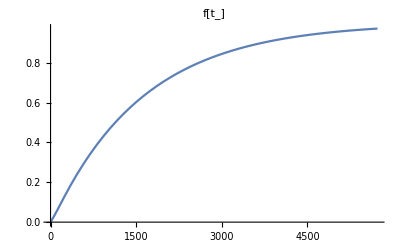

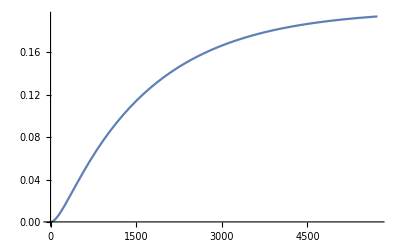

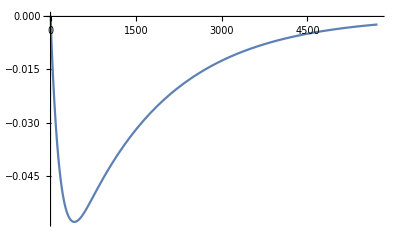

```mathematica
Γ=1000; (*position dans la colonne*)
f[t_]=(Cco2[n/2][t])/(Hco2 Patm yco2[0][t])/.sol;
g[t_]=yco2[n/2][t]/.sol;
h[t_]= (Hco2 Patm yco2[n/2][t]-Cco2[n/2][t])/(Hco2 Patm yco2[0][t])/.sol;
Plot[f[t],{t,0,ψ τcg},PlotRange->All, PlotLabel->"f[t_]"]
Plot[g[t],{t,0,ψ τcg},PlotRange->All]
Plot[h[t],{t,0,ψ τcg},PlotRange->All]
(*,PlotLabel->"Variation de la fraction molaire à mi-hauteur en fonction du temps",AxesLabel->{"Temps en seconde","Fraction molaire"},Frame->True,PlotRange->All,FrameStyle->Directive[Thick,Black],GridLines->Automatic]*)
```